# BTC-USD Drawdowns

```mathematica
Clear["Global`"];
SetDirectory[NotebookDirectory[]];
(*Buttons to hide/show code*)CloseAllInputsCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];
SetOptions[#,CellOpen->False]&/@cells;];

OpenAllInputsCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];
SetOptions[#,CellOpen->True]&/@cells;];

Row[{Button["Hide Code",SelectionEvaluate[CloseAllInputsCells[]]],Button["Show Code",SelectionEvaluate[OpenAllInputsCells[]]]}]
```

Hide CodeShow Code

```mathematica
(* Function shortcuts *)
st=StringTemplate;
dollar[a_]:=st["$``"][NumberForm[a,DigitBlock->3]];
(* Default properties for generated plots *)
imagesize=1000;
imagemargins=20;
labelstyle=Directive[14];
titlestyle={20,Red};
subtitlestyle = {15};
plotbackground=Lighter[LightGray,0.75];
updatedstr=Style[st["(updated: ``)"][DateString[]],subtitlestyle];
maniprange=Join[{1,2,3, 6, 9},Range[12,144,6]]//Reverse;
(*origindate="Sep. 14, 2011";*)
origindate="Mar. 28, 2015";
btcusd =FinancialData["BTC/USD",origindate];
nbtcusd=btcusd//Normal;
currentprice=Last[Last[nbtcusd]];
```

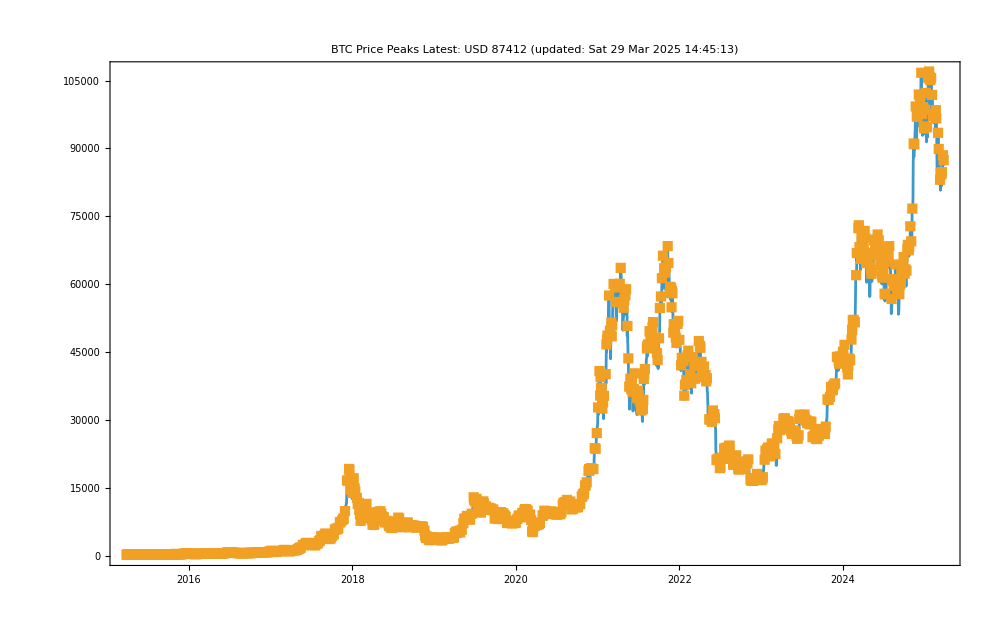

```mathematica
sigma=0;
peaks=FindPeaks[TimeSeriesResample[btcusd],sigma];
(*valleys=TimeSeriesMap[
Times[-1,#]&
,FindPeaks[
TimeSeriesResample[TimeSeriesMap[Times[-1,#]&,btcusd]]
,sigma
]
];*)
DateListPlot[
{btcusd,peaks}
,Joined->{True,False,False}
,PlotMarkers->{None,Automatic,Automatic}
,ImageSize->imagesize
,GridLines->Automatic
,PlotLabel->Column[
{
Style[
"BTC Price Peaks"
,titlestyle
]
,Style[
"Latest: USD " <> ToString[btcusd["LastValue"]//Round]
,subtitlestyle
]
,updatedstr
}
,Center
]
]
```

```mathematica
peaks
```

TimeSeries[…]

```mathematica
Max[peaks]
```

107000.

```mathematica
TimeSeriesSelect=ResourceFunction["TimeSeriesSelect"];
newpeaks=Block[{i=-∞},TimeSeriesSelect[peaks,(#2>i&&(i=#2)==i&)]];
```

```mathematica
TimeSeriesMap[f,newpeaks]["DatePath"]
```

{{Sun 29 Mar 2015 00:00:00GMT-4,f[252.68]},{Sat 4 Apr 2015 00:00:00GMT-4,f[254.11]},{Tue 7 Apr 2015 00:00:00GMT-4,f[255.97]},{Wed 1 Jul 2015 00:00:00GMT-4,f[263.44]},{Tue 7 Jul 2015 00:00:00GMT-4,f[274.515]},{Mon 13 Jul 2015 00:00:00GMT-4,f[307.181]},{Sat 31 Oct 2015 00:00:00GMT-4,f[328.365]},{Wed 4 Nov 2015 00:00:00GMT-4,f[402.535]},{Thu 10 Dec 2015 00:00:00GMT-4,f[417.305]},{Sat 12 Dec 2015 00:00:00GMT-4,f[450.65]},{Wed 16 Dec 2015 00:00:00GMT-4,f[464.545]},{Wed 27 Apr 2016 00:00:00GMT-4,f[467.365]},{Sun 29 May 2016 00:00:00GMT-4,f[522.705]},{Thu 2 Jun 2016 00:00:00GMT-4,f[536.915]},{Sat 4 Jun 2016 00:00:00GMT-4,f[569.025]},{Tue 7 Jun 2016 00:00:00GMT-4,f[583.745]},{Mon 20 Jun 2016 00:00:00GMT-4,f[760.75]},{Sat 3 Dec 2016 00:00:00GMT-4,f[769.985]},{Sun 11 Dec 2016 00:00:00GMT-4,f[773.875]},{Wed 14 Dec 2016 00:00:00GMT-4,f[777.75]},{Sun 18 Dec 2016 00:00:00GMT-4,f[788.855]},{Sat 24 Dec 2016 00:00:00GMT-4,f[914.24]},{Thu 29 Dec 2016 00:00:00GMT-4,f[972.245]},{Thu 5 Jan 2017 00:00:00GMT-4,f[1127.02]},{Sat 25 Feb 2017 00:00:00GMT-4,f[1182.54]},{Sat 4 Mar 2017 00:00:00GMT-4,f[1287.26]},{Fri 28 Apr 2017 00:00:00GMT-4,f[1331.18]},{Wed 3 May 2017 00:00:00GMT-4,f[1447.65]},{Fri 5 May 2017 00:00:00GMT-4,f[1538.46]},{Tue 9 May 2017 00:00:00GMT-4,f[1632.51]},{Fri 12 May 2017 00:00:00GMT-4,f[1777.]},{Mon 15 May 2017 00:00:00GMT-4,f[1781.21]},{Thu 25 May 2017 00:00:00GMT-4,f[2403.37]},{Sun 4 Jun 2017 00:00:00GMT-4,f[2474.01]},{Wed 7 Jun 2017 00:00:00GMT-4,f[2757.55]},{Mon 12 Jun 2017 00:00:00GMT-4,f[2863.5]},{Tue 1 Aug 2017 00:00:00GMT-4,f[2872.68]},{Sun 6 Aug 2017 00:00:00GMT-4,f[3255.64]},{Wed 9 Aug 2017 00:00:00GMT-4,f[3410.76]},{Tue 15 Aug 2017 00:00:00GMT-4,f[4320.27]},{Thu 17 Aug 2017 00:00:00GMT-4,f[4367.75]},{Wed 30 Aug 2017 00:00:00GMT-4,f[4577.75]},{Sat 2 Sep 2017 00:00:00GMT-4,f[4921.83]},{Sun 15 Oct 2017 00:00:00GMT-4,f[5796.96]},{Sun 22 Oct 2017 00:00:00GMT-4,f[6007.97]},{Mon 30 Oct 2017 00:00:00GMT-4,f[6142.15]},{Mon 6 Nov 2017 00:00:00GMT-4,f[7378.92]},{Thu 9 Nov 2017 00:00:00GMT-4,f[7460.98]},{Fri 17 Nov 2017 00:00:00GMT-4,f[7849.64]},{Tue 21 Nov 2017 00:00:00GMT-4,f[8213.67]},{Wed 29 Nov 2017 00:00:00GMT-4,f[9867.62]},{Fri 8 Dec 2017 00:00:00GMT-4,f[16615.5]},{Wed 13 Dec 2017 00:00:00GMT-4,f[16662.9]},{Sun 17 Dec 2017 00:00:00GMT-4,f[19183.4]},{Mon 30 Nov 2020 00:00:00GMT-4,f[19254.1]},{Thu 3 Dec 2020 00:00:00GMT-4,f[19360.9]},{Sat 19 Dec 2020 00:00:00GMT-4,f[23778.5]},{Mon 28 Dec 2020 00:00:00GMT-4,f[27112.2]},{Sun 3 Jan 2021 00:00:00GMT-4,f[32780.3]},{Sat 9 Jan 2021 00:00:00GMT-4,f[40812.4]},{Tue 9 Feb 2021 00:00:00GMT-4,f[46695.2]},{Fri 12 Feb 2021 00:00:00GMT-4,f[47782.1]},{Sun 14 Feb 2021 00:00:00GMT-4,f[48661.9]},{Sun 21 Feb 2021 00:00:00GMT-4,f[57502.]},{Sat 13 Mar 2021 00:00:00GMT-4,f[60073.8]},{Sat 10 Apr 2021 00:00:00GMT-4,f[60100.8]},{Wed 14 Apr 2021 00:00:00GMT-4,f[63611.3]},{Wed 20 Oct 2021 00:00:00GMT-4,f[66290.3]},{Wed 10 Nov 2021 00:00:00GMT-4,f[68420.7]},{Mon 11 Mar 2024 00:00:00GMT-4,f[72362.9]},{Wed 13 Mar 2024 00:00:00GMT-4,f[73025.9]},{Thu 7 Nov 2024 00:00:00GMT-4,f[76708.8]},{Wed 13 Nov 2024 00:00:00GMT-4,f[91093.7]},{Fri 22 Nov 2024 00:00:00GMT-4,f[99273.3]},{Fri 6 Dec 2024 00:00:00GMT-4,f[101916.]},{Tue 17 Dec 2024 00:00:00GMT-4,f[106717.]},{Tue 21 Jan 2025 00:00:00GMT-4,f[107000.]}}

```mathematica
newpeaks//Normal
```

{{Sun 29 Mar 2015 00:00:00GMT-4,252.68},{Sat 4 Apr 2015 00:00:00GMT-4,254.11},{Tue 7 Apr 2015 00:00:00GMT-4,255.97},{Wed 1 Jul 2015 00:00:00GMT-4,263.44},{Tue 7 Jul 2015 00:00:00GMT-4,274.515},{Mon 13 Jul 2015 00:00:00GMT-4,307.181},{Sat 31 Oct 2015 00:00:00GMT-4,328.365},{Wed 4 Nov 2015 00:00:00GMT-4,402.535},{Thu 10 Dec 2015 00:00:00GMT-4,417.305},{Sat 12 Dec 2015 00:00:00GMT-4,450.65},{Wed 16 Dec 2015 00:00:00GMT-4,464.545},{Wed 27 Apr 2016 00:00:00GMT-4,467.365},{Sun 29 May 2016 00:00:00GMT-4,522.705},{Thu 2 Jun 2016 00:00:00GMT-4,536.915},{Sat 4 Jun 2016 00:00:00GMT-4,569.025},{Tue 7 Jun 2016 00:00:00GMT-4,583.745},{Mon 20 Jun 2016 00:00:00GMT-4,760.75},{Sat 3 Dec 2016 00:00:00GMT-4,769.985},{Sun 11 Dec 2016 00:00:00GMT-4,773.875},{Wed 14 Dec 2016 00:00:00GMT-4,777.75},{Sun 18 Dec 2016 00:00:00GMT-4,788.855},{Sat 24 Dec 2016 00:00:00GMT-4,914.24},{Thu 29 Dec 2016 00:00:00GMT-4,972.245},{Thu 5 Jan 2017 00:00:00GMT-4,1127.02},{Sat 25 Feb 2017 00:00:00GMT-4,1182.54},{Sat 4 Mar 2017 00:00:00GMT-4,1287.26},{Fri 28 Apr 2017 00:00:00GMT-4,1331.18},{Wed 3 May 2017 00:00:00GMT-4,1447.65},{Fri 5 May 2017 00:00:00GMT-4,1538.46},{Tue 9 May 2017 00:00:00GMT-4,1632.51},{Fri 12 May 2017 00:00:00GMT-4,1777.},{Mon 15 May 2017 00:00:00GMT-4,1781.21},{Thu 25 May 2017 00:00:00GMT-4,2403.37},{Sun 4 Jun 2017 00:00:00GMT-4,2474.01},{Wed 7 Jun 2017 00:00:00GMT-4,2757.55},{Mon 12 Jun 2017 00:00:00GMT-4,2863.5},{Tue 1 Aug 2017 00:00:00GMT-4,2872.68},{Sun 6 Aug 2017 00:00:00GMT-4,3255.64},{Wed 9 Aug 2017 00:00:00GMT-4,3410.76},{Tue 15 Aug 2017 00:00:00GMT-4,4320.27},{Thu 17 Aug 2017 00:00:00GMT-4,4367.75},{Wed 30 Aug 2017 00:00:00GMT-4,4577.75},{Sat 2 Sep 2017 00:00:00GMT-4,4921.83},{Sun 15 Oct 2017 00:00:00GMT-4,5796.96},{Sun 22 Oct 2017 00:00:00GMT-4,6007.97},{Mon 30 Oct 2017 00:00:00GMT-4,6142.15},{Mon 6 Nov 2017 00:00:00GMT-4,7378.92},{Thu 9 Nov 2017 00:00:00GMT-4,7460.98},{Fri 17 Nov 2017 00:00:00GMT-4,7849.64},{Tue 21 Nov 2017 00:00:00GMT-4,8213.67},{Wed 29 Nov 2017 00:00:00GMT-4,9867.62},{Fri 8 Dec 2017 00:00:00GMT-4,16615.5},{Wed 13 Dec 2017 00:00:00GMT-4,16662.9},{Sun 17 Dec 2017 00:00:00GMT-4,19183.4},{Mon 30 Nov 2020 00:00:00GMT-4,19254.1},{Thu 3 Dec 2020 00:00:00GMT-4,19360.9},{Sat 19 Dec 2020 00:00:00GMT-4,23778.5},{Mon 28 Dec 2020 00:00:00GMT-4,27112.2},{Sun 3 Jan 2021 00:00:00GMT-4,32780.3},{Sat 9 Jan 2021 00:00:00GMT-4,40812.4},{Tue 9 Feb 2021 00:00:00GMT-4,46695.2},{Fri 12 Feb 2021 00:00:00GMT-4,47782.1},{Sun 14 Feb 2021 00:00:00GMT-4,48661.9},{Sun 21 Feb 2021 00:00:00GMT-4,57502.},{Sat 13 Mar 2021 00:00:00GMT-4,60073.8},{Sat 10 Apr 2021 00:00:00GMT-4,60100.8},{Wed 14 Apr 2021 00:00:00GMT-4,63611.3},{Wed 20 Oct 2021 00:00:00GMT-4,66290.3},{Wed 10 Nov 2021 00:00:00GMT-4,68420.7},{Mon 11 Mar 2024 00:00:00GMT-4,72362.9},{Wed 13 Mar 2024 00:00:00GMT-4,73025.9},{Thu 7 Nov 2024 00:00:00GMT-4,76708.8},{Wed 13 Nov 2024 00:00:00GMT-4,91093.7},{Fri 22 Nov 2024 00:00:00GMT-4,99273.3},{Fri 6 Dec 2024 00:00:00GMT-4,101916.},{Tue 17 Dec 2024 00:00:00GMT-4,106717.},{Tue 21 Jan 2025 00:00:00GMT-4,107000.}}

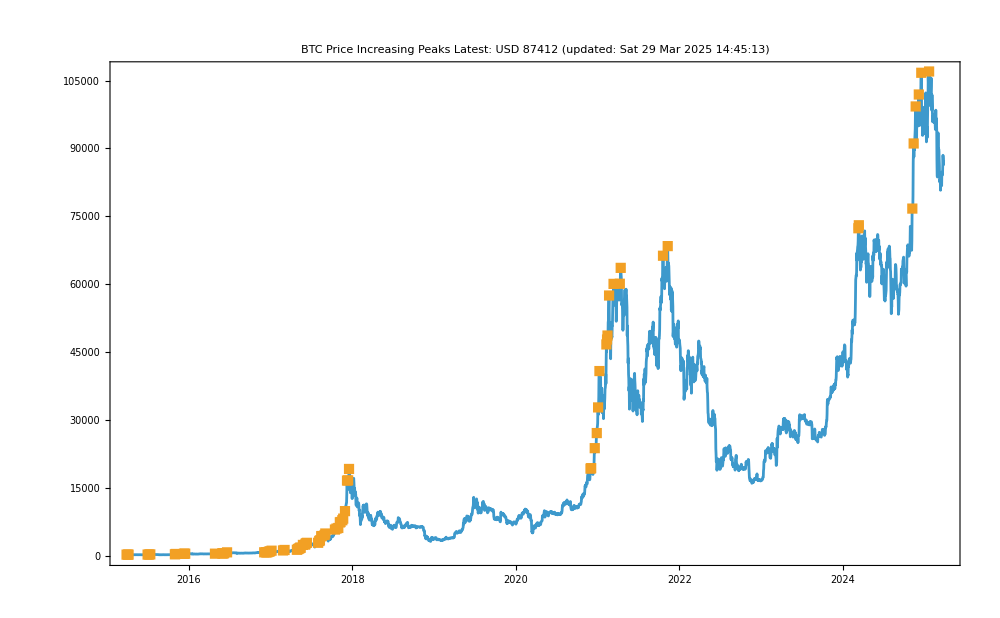

```mathematica
DateListPlot[
{btcusd,newpeaks}
,Joined->{True,False}
,PlotMarkers->{None,Automatic,Automatic}
,ImageSize->imagesize
,GridLines->Automatic
,PlotLabel->Column[
{
Style[
"BTC Price Increasing Peaks"
,titlestyle
]
,Style[
"Latest: USD " <> ToString[btcusd["LastValue"]//Round]
,subtitlestyle
]
,updatedstr
}
,Center
]
]
```

```mathematica
Column[
{#,TimeSeriesWindow[btcusd,{#[[1]],Now}]//Min}&/@(newpeaks//Normal)
]
```

{{Sun 29 Mar 2015 00:00:00GMT-4,252.68},211.285}
{{Sat 4 Apr 2015 00:00:00GMT-4,254.11},211.285}
{{Tue 7 Apr 2015 00:00:00GMT-4,255.97},211.285}
{{Wed 1 Jul 2015 00:00:00GMT-4,263.44},211.285}
{{Tue 7 Jul 2015 00:00:00GMT-4,274.515},211.285}
{{Mon 13 Jul 2015 00:00:00GMT-4,307.181},211.285}
{{Sat 31 Oct 2015 00:00:00GMT-4,328.365},302.985}
{{Wed 4 Nov 2015 00:00:00GMT-4,402.535},302.985}
{{Thu 10 Dec 2015 00:00:00GMT-4,417.305},360.385}
{{Sat 12 Dec 2015 00:00:00GMT-4,450.65},360.385}
{{Wed 16 Dec 2015 00:00:00GMT-4,464.545},360.385}
{{Wed 27 Apr 2016 00:00:00GMT-4,467.365},437.61}
{{Sun 29 May 2016 00:00:00GMT-4,522.705},486.425}
{{Thu 2 Jun 2016 00:00:00GMT-4,536.915},486.425}
{{Sat 4 Jun 2016 00:00:00GMT-4,569.025},486.425}
{{Tue 7 Jun 2016 00:00:00GMT-4,583.745},486.425}
{{Mon 20 Jun 2016 00:00:00GMT-4,760.75},486.425}
{{Sat 3 Dec 2016 00:00:00GMT-4,769.985},750.605}
{{Sun 11 Dec 2016 00:00:00GMT-4,773.875},768.185}
{{Wed 14 Dec 2016 00:00:00GMT-4,777.75},774.53}
{{Sun 18 Dec 2016 00:00:00GMT-4,788.855},782.35}
{{Sat 24 Dec 2016 00:00:00GMT-4,914.24},782.35}
{{Thu 29 Dec 2016 00:00:00GMT-4,972.245},782.35}
{{Thu 5 Jan 2017 00:00:00GMT-4,1127.02},782.35}
{{Sat 25 Feb 2017 00:00:00GMT-4,1182.54},933.915}
{{Sat 4 Mar 2017 00:00:00GMT-4,1287.26},933.915}
{{Fri 28 Apr 2017 00:00:00GMT-4,1331.18},1293.28}
{{Wed 3 May 2017 00:00:00GMT-4,1447.65},1383.82}
{{Fri 5 May 2017 00:00:00GMT-4,1538.46},1435.07}
{{Tue 9 May 2017 00:00:00GMT-4,1632.51},1613.66}
{{Fri 12 May 2017 00:00:00GMT-4,1777.},1665.46}
{{Mon 15 May 2017 00:00:00GMT-4,1781.21},1665.46}
{{Thu 25 May 2017 00:00:00GMT-4,2403.37},1918.68}
{{Sun 4 Jun 2017 00:00:00GMT-4,2474.01},1918.68}
{{Wed 7 Jun 2017 00:00:00GMT-4,2757.55},1918.68}
{{Mon 12 Jun 2017 00:00:00GMT-4,2863.5},1918.68}
{{Tue 1 Aug 2017 00:00:00GMT-4,2872.68},2702.09}
{{Sun 6 Aug 2017 00:00:00GMT-4,3255.64},3185.13}
{{Wed 9 Aug 2017 00:00:00GMT-4,3410.76},3185.13}
{{Tue 15 Aug 2017 00:00:00GMT-4,4320.27},3185.13}
{{Thu 17 Aug 2017 00:00:00GMT-4,4367.75},3185.13}
{{Wed 30 Aug 2017 00:00:00GMT-4,4577.75},3185.13}
{{Sat 2 Sep 2017 00:00:00GMT-4,4921.83},3185.13}
{{Sun 15 Oct 2017 00:00:00GMT-4,5796.96},3185.13}
{{Sun 22 Oct 2017 00:00:00GMT-4,6007.97},3185.13}
{{Mon 30 Oct 2017 00:00:00GMT-4,6142.15},3185.13}
{{Mon 6 Nov 2017 00:00:00GMT-4,7378.92},3185.13}
{{Thu 9 Nov 2017 00:00:00GMT-4,7460.98},3185.13}
{{Fri 17 Nov 2017 00:00:00GMT-4,7849.64},3185.13}
{{Tue 21 Nov 2017 00:00:00GMT-4,8213.67},3185.13}
{{Wed 29 Nov 2017 00:00:00GMT-4,9867.62},3185.13}
{{Fri 8 Dec 2017 00:00:00GMT-4,16615.5},3185.13}
{{Wed 13 Dec 2017 00:00:00GMT-4,16662.9},3185.13}
{{Sun 17 Dec 2017 00:00:00GMT-4,19183.4},3185.13}
{{Mon 30 Nov 2020 00:00:00GMT-4,19254.1},16014.5}
{{Thu 3 Dec 2020 00:00:00GMT-4,19360.9},16014.5}
{{Sat 19 Dec 2020 00:00:00GMT-4,23778.5},16014.5}
{{Mon 28 Dec 2020 00:00:00GMT-4,27112.2},16014.5}
{{Sun 3 Jan 2021 00:00:00GMT-4,32780.3},16014.5}
{{Sat 9 Jan 2021 00:00:00GMT-4,40812.4},16014.5}
{{Tue 9 Feb 2021 00:00:00GMT-4,46695.2},16014.5}
{{Fri 12 Feb 2021 00:00:00GMT-4,47782.1},16014.5}
{{Sun 14 Feb 2021 00:00:00GMT-4,48661.9},16014.5}
{{Sun 21 Feb 2021 00:00:00GMT-4,57502.},16014.5}
{{Sat 13 Mar 2021 00:00:00GMT-4,60073.8},16014.5}
{{Sat 10 Apr 2021 00:00:00GMT-4,60100.8},16014.5}
{{Wed 14 Apr 2021 00:00:00GMT-4,63611.3},16014.5}
{{Wed 20 Oct 2021 00:00:00GMT-4,66290.3},16014.5}
{{Wed 10 Nov 2021 00:00:00GMT-4,68420.7},16014.5}
{{Mon 11 Mar 2024 00:00:00GMT-4,72362.9},53358.9}
{{Wed 13 Mar 2024 00:00:00GMT-4,73025.9},53358.9}
{{Thu 7 Nov 2024 00:00:00GMT-4,76708.8},76356.1}
{{Wed 13 Nov 2024 00:00:00GMT-4,91093.7},80762.1}
{{Fri 22 Nov 2024 00:00:00GMT-4,99273.3},80762.1}
{{Fri 6 Dec 2024 00:00:00GMT-4,101916.},80762.1}
{{Tue 17 Dec 2024 00:00:00GMT-4,106717.},80762.1}
{{Tue 21 Jan 2025 00:00:00GMT-4,107000.},80762.1}

```mathematica
pv=Last/@GatherBy[{#,TimeSeriesWindow[btcusd,{#[[1]],Now}]//Min}&/@(newpeaks//Normal),Last]
```

{{{Mon 13 Jul 2015 00:00:00GMT-4,307.181},211.285},{{Wed 4 Nov 2015 00:00:00GMT-4,402.535},302.985},{{Wed 16 Dec 2015 00:00:00GMT-4,464.545},360.385},{{Wed 27 Apr 2016 00:00:00GMT-4,467.365},437.61},{{Mon 20 Jun 2016 00:00:00GMT-4,760.75},486.425},{{Sat 3 Dec 2016 00:00:00GMT-4,769.985},750.605},{{Sun 11 Dec 2016 00:00:00GMT-4,773.875},768.185},{{Wed 14 Dec 2016 00:00:00GMT-4,777.75},774.53},{{Thu 5 Jan 2017 00:00:00GMT-4,1127.02},782.35},{{Sat 4 Mar 2017 00:00:00GMT-4,1287.26},933.915},{{Fri 28 Apr 2017 00:00:00GMT-4,1331.18},1293.28},{{Wed 3 May 2017 00:00:00GMT-4,1447.65},1383.82},{{Fri 5 May 2017 00:00:00GMT-4,1538.46},1435.07},{{Tue 9 May 2017 00:00:00GMT-4,1632.51},1613.66},{{Mon 15 May 2017 00:00:00GMT-4,1781.21},1665.46},{{Mon 12 Jun 2017 00:00:00GMT-4,2863.5},1918.68},{{Tue 1 Aug 2017 00:00:00GMT-4,2872.68},2702.09},{{Sun 17 Dec 2017 00:00:00GMT-4,19183.4},3185.13},{{Wed 10 Nov 2021 00:00:00GMT-4,68420.7},16014.5},{{Wed 13 Mar 2024 00:00:00GMT-4,73025.9},53358.9},{{Thu 7 Nov 2024 00:00:00GMT-4,76708.8},76356.1},{{Tue 21 Jan 2025 00:00:00GMT-4,107000.},80762.1}}

```mathematica
{First[#[[1]]],Last[#[[1]]],#[[2]],PercentForm[1-(#[[2]]/Last[#[[1]]])]}&/@ pv
```

{{Mon 13 Jul 2015 00:00:00GMT-4,307.181,211.285,31.22%},{Wed 4 Nov 2015 00:00:00GMT-4,402.535,302.985,24.73%},{Wed 16 Dec 2015 00:00:00GMT-4,464.545,360.385,22.42%},{Wed 27 Apr 2016 00:00:00GMT-4,467.365,437.61,6.367%},{Mon 20 Jun 2016 00:00:00GMT-4,760.75,486.425,36.06%},{Sat 3 Dec 2016 00:00:00GMT-4,769.985,750.605,2.517%},{Sun 11 Dec 2016 00:00:00GMT-4,773.875,768.185,0.7353%},{Wed 14 Dec 2016 00:00:00GMT-4,777.75,774.53,0.414%},{Thu 5 Jan 2017 00:00:00GMT-4,1127.02,782.35,30.58%},{Sat 4 Mar 2017 00:00:00GMT-4,1287.26,933.915,27.45%},{Fri 28 Apr 2017 00:00:00GMT-4,1331.18,1293.28,2.847%},{Wed 3 May 2017 00:00:00GMT-4,1447.65,1383.82,4.409%},{Fri 5 May 2017 00:00:00GMT-4,1538.46,1435.07,6.72%},{Tue 9 May 2017 00:00:00GMT-4,1632.51,1613.66,1.155%},{Mon 15 May 2017 00:00:00GMT-4,1781.21,1665.46,6.498%},{Mon 12 Jun 2017 00:00:00GMT-4,2863.5,1918.68,33%},{Tue 1 Aug 2017 00:00:00GMT-4,2872.68,2702.09,5.938%},{Sun 17 Dec 2017 00:00:00GMT-4,19183.4,3185.13,83.4%},{Wed 10 Nov 2021 00:00:00GMT-4,68420.7,16014.5,76.59%},{Wed 13 Mar 2024 00:00:00GMT-4,73025.9,53358.9,26.93%},{Thu 7 Nov 2024 00:00:00GMT-4,76708.8,76356.1,0.4598%},{Tue 21 Jan 2025 00:00:00GMT-4,107000.,80762.1,24.52%}}

```mathematica
ReverseSortBy[{First[#[[1]]],Last[#[[1]]],#[[2]],PercentForm[1-(#[[2]]/Last[#[[1]]])]}&/@ pv,Last]//Column
```

{Sun 17 Dec 2017 00:00:00GMT-4,19183.4,3185.13,83.4%}
{Wed 10 Nov 2021 00:00:00GMT-4,68420.7,16014.5,76.59%}
{Mon 20 Jun 2016 00:00:00GMT-4,760.75,486.425,36.06%}
{Mon 12 Jun 2017 00:00:00GMT-4,2863.5,1918.68,33%}
{Mon 13 Jul 2015 00:00:00GMT-4,307.181,211.285,31.22%}
{Thu 5 Jan 2017 00:00:00GMT-4,1127.02,782.35,30.58%}
{Sat 4 Mar 2017 00:00:00GMT-4,1287.26,933.915,27.45%}
{Wed 13 Mar 2024 00:00:00GMT-4,73025.9,53358.9,26.93%}
{Wed 4 Nov 2015 00:00:00GMT-4,402.535,302.985,24.73%}
{Tue 21 Jan 2025 00:00:00GMT-4,107000.,80762.1,24.52%}
{Wed 16 Dec 2015 00:00:00GMT-4,464.545,360.385,22.42%}
{Fri 5 May 2017 00:00:00GMT-4,1538.46,1435.07,6.72%}
{Mon 15 May 2017 00:00:00GMT-4,1781.21,1665.46,6.498%}
{Wed 27 Apr 2016 00:00:00GMT-4,467.365,437.61,6.367%}
{Tue 1 Aug 2017 00:00:00GMT-4,2872.68,2702.09,5.938%}
{Wed 3 May 2017 00:00:00GMT-4,1447.65,1383.82,4.409%}
{Fri 28 Apr 2017 00:00:00GMT-4,1331.18,1293.28,2.847%}
{Sat 3 Dec 2016 00:00:00GMT-4,769.985,750.605,2.517%}
{Tue 9 May 2017 00:00:00GMT-4,1632.51,1613.66,1.155%}
{Sun 11 Dec 2016 00:00:00GMT-4,773.875,768.185,0.7353%}
{Thu 7 Nov 2024 00:00:00GMT-4,76708.8,76356.1,0.4598%}
{Wed 14 Dec 2016 00:00:00GMT-4,777.75,774.53,0.414%}

### alternate path

```mathematica
{#,TimeSeriesWindow[btcusd,{#[[1]],Now}]//Min}&/@(newpeaks//Normal)
```

{{{Sun 29 Mar 2015 00:00:00GMT-4,252.68},211.285},{{Sat 4 Apr 2015 00:00:00GMT-4,254.11},211.285},{{Tue 7 Apr 2015 00:00:00GMT-4,255.97},211.285},{{Wed 1 Jul 2015 00:00:00GMT-4,263.44},211.285},{{Tue 7 Jul 2015 00:00:00GMT-4,274.515},211.285},{{Mon 13 Jul 2015 00:00:00GMT-4,307.181},211.285},{{Sat 31 Oct 2015 00:00:00GMT-4,328.365},302.985},{{Wed 4 Nov 2015 00:00:00GMT-4,402.535},302.985},{{Thu 10 Dec 2015 00:00:00GMT-4,417.305},360.385},{{Sat 12 Dec 2015 00:00:00GMT-4,450.65},360.385},{{Wed 16 Dec 2015 00:00:00GMT-4,464.545},360.385},{{Wed 27 Apr 2016 00:00:00GMT-4,467.365},437.61},{{Sun 29 May 2016 00:00:00GMT-4,522.705},486.425},{{Thu 2 Jun 2016 00:00:00GMT-4,536.915},486.425},{{Sat 4 Jun 2016 00:00:00GMT-4,569.025},486.425},{{Tue 7 Jun 2016 00:00:00GMT-4,583.745},486.425},{{Mon 20 Jun 2016 00:00:00GMT-4,760.75},486.425},{{Sat 3 Dec 2016 00:00:00GMT-4,769.985},750.605},{{Sun 11 Dec 2016 00:00:00GMT-4,773.875},768.185},{{Wed 14 Dec 2016 00:00:00GMT-4,777.75},774.53},{{Sun 18 Dec 2016 00:00:00GMT-4,788.855},782.35},{{Sat 24 Dec 2016 00:00:00GMT-4,914.24},782.35},{{Thu 29 Dec 2016 00:00:00GMT-4,972.245},782.35},{{Thu 5 Jan 2017 00:00:00GMT-4,1127.02},782.35},{{Sat 25 Feb 2017 00:00:00GMT-4,1182.54},933.915},{{Sat 4 Mar 2017 00:00:00GMT-4,1287.26},933.915},{{Fri 28 Apr 2017 00:00:00GMT-4,1331.18},1293.28},{{Wed 3 May 2017 00:00:00GMT-4,1447.65},1383.82},{{Fri 5 May 2017 00:00:00GMT-4,1538.46},1435.07},{{Tue 9 May 2017 00:00:00GMT-4,1632.51},1613.66},{{Fri 12 May 2017 00:00:00GMT-4,1777.},1665.46},{{Mon 15 May 2017 00:00:00GMT-4,1781.21},1665.46},{{Thu 25 May 2017 00:00:00GMT-4,2403.37},1918.68},{{Sun 4 Jun 2017 00:00:00GMT-4,2474.01},1918.68},{{Wed 7 Jun 2017 00:00:00GMT-4,2757.55},1918.68},{{Mon 12 Jun 2017 00:00:00GMT-4,2863.5},1918.68},{{Tue 1 Aug 2017 00:00:00GMT-4,2872.68},2702.09},{{Sun 6 Aug 2017 00:00:00GMT-4,3255.64},3185.13},{{Wed 9 Aug 2017 00:00:00GMT-4,3410.76},3185.13},{{Tue 15 Aug 2017 00:00:00GMT-4,4320.27},3185.13},{{Thu 17 Aug 2017 00:00:00GMT-4,4367.75},3185.13},{{Wed 30 Aug 2017 00:00:00GMT-4,4577.75},3185.13},{{Sat 2 Sep 2017 00:00:00GMT-4,4921.83},3185.13},{{Sun 15 Oct 2017 00:00:00GMT-4,5796.96},3185.13},{{Sun 22 Oct 2017 00:00:00GMT-4,6007.97},3185.13},{{Mon 30 Oct 2017 00:00:00GMT-4,6142.15},3185.13},{{Mon 6 Nov 2017 00:00:00GMT-4,7378.92},3185.13},{{Thu 9 Nov 2017 00:00:00GMT-4,7460.98},3185.13},{{Fri 17 Nov 2017 00:00:00GMT-4,7849.64},3185.13},{{Tue 21 Nov 2017 00:00:00GMT-4,8213.67},3185.13},{{Wed 29 Nov 2017 00:00:00GMT-4,9867.62},3185.13},{{Fri 8 Dec 2017 00:00:00GMT-4,16615.5},3185.13},{{Wed 13 Dec 2017 00:00:00GMT-4,16662.9},3185.13},{{Sun 17 Dec 2017 00:00:00GMT-4,19183.4},3185.13},{{Mon 30 Nov 2020 00:00:00GMT-4,19254.1},16014.5},{{Thu 3 Dec 2020 00:00:00GMT-4,19360.9},16014.5},{{Sat 19 Dec 2020 00:00:00GMT-4,23778.5},16014.5},{{Mon 28 Dec 2020 00:00:00GMT-4,27112.2},16014.5},{{Sun 3 Jan 2021 00:00:00GMT-4,32780.3},16014.5},{{Sat 9 Jan 2021 00:00:00GMT-4,40812.4},16014.5},{{Tue 9 Feb 2021 00:00:00GMT-4,46695.2},16014.5},{{Fri 12 Feb 2021 00:00:00GMT-4,47782.1},16014.5},{{Sun 14 Feb 2021 00:00:00GMT-4,48661.9},16014.5},{{Sun 21 Feb 2021 00:00:00GMT-4,57502.},16014.5},{{Sat 13 Mar 2021 00:00:00GMT-4,60073.8},16014.5},{{Sat 10 Apr 2021 00:00:00GMT-4,60100.8},16014.5},{{Wed 14 Apr 2021 00:00:00GMT-4,63611.3},16014.5},{{Wed 20 Oct 2021 00:00:00GMT-4,66290.3},16014.5},{{Wed 10 Nov 2021 00:00:00GMT-4,68420.7},16014.5},{{Mon 11 Mar 2024 00:00:00GMT-4,72362.9},53358.9},{{Wed 13 Mar 2024 00:00:00GMT-4,73025.9},53358.9},{{Thu 7 Nov 2024 00:00:00GMT-4,76708.8},76356.1},{{Wed 13 Nov 2024 00:00:00GMT-4,91093.7},80762.1},{{Fri 22 Nov 2024 00:00:00GMT-4,99273.3},80762.1},{{Fri 6 Dec 2024 00:00:00GMT-4,101916.},80762.1},{{Tue 17 Dec 2024 00:00:00GMT-4,106717.},80762.1},{{Tue 21 Jan 2025 00:00:00GMT-4,107000.},80762.1}}

```mathematica
{#,low=TimeSeriesWindow[btcusd,{#[[1]],Now}]//Min;Cases[Normal[TimeSeriesWindow[btcusd,{#[[1]],Now}]],{_,low}]}&/@(newpeaks//Normal)
```

{{{Sun 29 Mar 2015 00:00:00GMT-4,252.68},{{Tue 25 Aug 2015 00:00:00GMT-4,211.285}}},{{Sat 4 Apr 2015 00:00:00GMT-4,254.11},{{Tue 25 Aug 2015 00:00:00GMT-4,211.285}}},{{Tue 7 Apr 2015 00:00:00GMT-4,255.97},{{Tue 25 Aug 2015 00:00:00GMT-4,211.285}}},{{Wed 1 Jul 2015 00:00:00GMT-4,263.44},{{Tue 25 Aug 2015 00:00:00GMT-4,211.285}}},{{Tue 7 Jul 2015 00:00:00GMT-4,274.515},{{Tue 25 Aug 2015 00:00:00GMT-4,211.285}}},{{Mon 13 Jul 2015 00:00:00GMT-4,307.181},{{Tue 25 Aug 2015 00:00:00GMT-4,211.285}}},{{Sat 31 Oct 2015 00:00:00GMT-4,328.365},{{Thu 12 Nov 2015 00:00:00GMT-4,302.985}}},{{Wed 4 Nov 2015 00:00:00GMT-4,402.535},{{Thu 12 Nov 2015 00:00:00GMT-4,302.985}}},{{Thu 10 Dec 2015 00:00:00GMT-4,417.305},{{Sat 16 Jan 2016 00:00:00GMT-4,360.385}}},{{Sat 12 Dec 2015 00:00:00GMT-4,450.65},{{Sat 16 Jan 2016 00:00:00GMT-4,360.385}}},{{Wed 16 Dec 2015 00:00:00GMT-4,464.545},{{Sat 16 Jan 2016 00:00:00GMT-4,360.385}}},{{Wed 27 Apr 2016 00:00:00GMT-4,467.365},{{Fri 20 May 2016 00:00:00GMT-4,437.61}}},{{Sun 29 May 2016 00:00:00GMT-4,522.705},{{Wed 3 Aug 2016 00:00:00GMT-4,486.425}}},{{Thu 2 Jun 2016 00:00:00GMT-4,536.915},{{Wed 3 Aug 2016 00:00:00GMT-4,486.425}}},{{Sat 4 Jun 2016 00:00:00GMT-4,569.025},{{Wed 3 Aug 2016 00:00:00GMT-4,486.425}}},{{Tue 7 Jun 2016 00:00:00GMT-4,583.745},{{Wed 3 Aug 2016 00:00:00GMT-4,486.425}}},{{Mon 20 Jun 2016 00:00:00GMT-4,760.75},{{Wed 3 Aug 2016 00:00:00GMT-4,486.425}}},{{Sat 3 Dec 2016 00:00:00GMT-4,769.985},{{Tue 6 Dec 2016 00:00:00GMT-4,750.605}}},{{Sun 11 Dec 2016 00:00:00GMT-4,773.875},{{Mon 12 Dec 2016 00:00:00GMT-4,768.185}}},{{Wed 14 Dec 2016 00:00:00GMT-4,777.75},{{Fri 16 Dec 2016 00:00:00GMT-4,774.53}}},{{Sun 18 Dec 2016 00:00:00GMT-4,788.855},{{Thu 12 Jan 2017 00:00:00GMT-4,782.35}}},{{Sat 24 Dec 2016 00:00:00GMT-4,914.24},{{Thu 12 Jan 2017 00:00:00GMT-4,782.35}}},{{Thu 29 Dec 2016 00:00:00GMT-4,972.245},{{Thu 12 Jan 2017 00:00:00GMT-4,782.35}}},{{Thu 5 Jan 2017 00:00:00GMT-4,1127.02},{{Thu 12 Jan 2017 00:00:00GMT-4,782.35}}},{{Sat 25 Feb 2017 00:00:00GMT-4,1182.54},{{Sat 25 Mar 2017 00:00:00GMT-4,933.915}}},{{Sat 4 Mar 2017 00:00:00GMT-4,1287.26},{{Sat 25 Mar 2017 00:00:00GMT-4,933.915}}},{{Fri 28 Apr 2017 00:00:00GMT-4,1331.18},{{Sun 30 Apr 2017 00:00:00GMT-4,1293.28}}},{{Wed 3 May 2017 00:00:00GMT-4,1447.65},{{Thu 4 May 2017 00:00:00GMT-4,1383.82}}},{{Fri 5 May 2017 00:00:00GMT-4,1538.46},{{Sat 6 May 2017 00:00:00GMT-4,1435.07}}},{{Tue 9 May 2017 00:00:00GMT-4,1632.51},{{Wed 10 May 2017 00:00:00GMT-4,1613.66}}},{{Fri 12 May 2017 00:00:00GMT-4,1777.},{{Tue 16 May 2017 00:00:00GMT-4,1665.46}}},{{Mon 15 May 2017 00:00:00GMT-4,1781.21},{{Tue 16 May 2017 00:00:00GMT-4,1665.46}}},{{Thu 25 May 2017 00:00:00GMT-4,2403.37},{{Mon 17 Jul 2017 00:00:00GMT-4,1918.68}}},{{Sun 4 Jun 2017 00:00:00GMT-4,2474.01},{{Mon 17 Jul 2017 00:00:00GMT-4,1918.68}}},{{Wed 7 Jun 2017 00:00:00GMT-4,2757.55},{{Mon 17 Jul 2017 00:00:00GMT-4,1918.68}}},{{Mon 12 Jun 2017 00:00:00GMT-4,2863.5},{{Mon 17 Jul 2017 00:00:00GMT-4,1918.68}}},{{Tue 1 Aug 2017 00:00:00GMT-4,2872.68},{{Thu 3 Aug 2017 00:00:00GMT-4,2702.09}}},{{Sun 6 Aug 2017 00:00:00GMT-4,3255.64},{{Sun 16 Dec 2018 00:00:00GMT-4,3185.13}}},{{Wed 9 Aug 2017 00:00:00GMT-4,3410.76},{{Sun 16 Dec 2018 00:00:00GMT-4,3185.13}}},{{Tue 15 Aug 2017 00:00:00GMT-4,4320.27},{{Sun 16 Dec 2018 00:00:00GMT-4,3185.13}}},{{Thu 17 Aug 2017 00:00:00GMT-4,4367.75},{{Sun 16 Dec 2018 00:00:00GMT-4,3185.13}}},{{Wed 30 Aug 2017 00:00:00GMT-4,4577.75},{{Sun 16 Dec 2018 00:00:00GMT-4,3185.13}}},{{Sat 2 Sep 2017 00:00:00GMT-4,4921.83},{{Sun 16 Dec 2018 00:00:00GMT-4,3185.13}}},{{Sun 15 Oct 2017 00:00:00GMT-4,5796.96},{{Sun 16 Dec 2018 00:00:00GMT-4,3185.13}}},{{Sun 22 Oct 2017 00:00:00GMT-4,6007.97},{{Sun 16 Dec 2018 00:00:00GMT-4,3185.13}}},{{Mon 30 Oct 2017 00:00:00GMT-4,6142.15},{{Sun 16 Dec 2018 00:00:00GMT-4,3185.13}}},{{Mon 6 Nov 2017 00:00:00GMT-4,7378.92},{{Sun 16 Dec 2018 00:00:00GMT-4,3185.13}}},{{Thu 9 Nov 2017 00:00:00GMT-4,7460.98},{{Sun 16 Dec 2018 00:00:00GMT-4,3185.13}}},{{Fri 17 Nov 2017 00:00:00GMT-4,7849.64},{{Sun 16 Dec 2018 00:00:00GMT-4,3185.13}}},{{Tue 21 Nov 2017 00:00:00GMT-4,8213.67},{{Sun 16 Dec 2018 00:00:00GMT-4,3185.13}}},{{Wed 29 Nov 2017 00:00:00GMT-4,9867.62},{{Sun 16 Dec 2018 00:00:00GMT-4,3185.13}}},{{Fri 8 Dec 2017 00:00:00GMT-4,16615.5},{{Sun 16 Dec 2018 00:00:00GMT-4,3185.13}}},{{Wed 13 Dec 2017 00:00:00GMT-4,16662.9},{{Sun 16 Dec 2018 00:00:00GMT-4,3185.13}}},{{Sun 17 Dec 2017 00:00:00GMT-4,19183.4},{{Sun 16 Dec 2018 00:00:00GMT-4,3185.13}}},{{Mon 30 Nov 2020 00:00:00GMT-4,19254.1},{{Mon 21 Nov 2022 00:00:00GMT-4,16014.5}}},{{Thu 3 Dec 2020 00:00:00GMT-4,19360.9},{{Mon 21 Nov 2022 00:00:00GMT-4,16014.5}}},{{Sat 19 Dec 2020 00:00:00GMT-4,23778.5},{{Mon 21 Nov 2022 00:00:00GMT-4,16014.5}}},{{Mon 28 Dec 2020 00:00:00GMT-4,27112.2},{{Mon 21 Nov 2022 00:00:00GMT-4,16014.5}}},{{Sun 3 Jan 2021 00:00:00GMT-4,32780.3},{{Mon 21 Nov 2022 00:00:00GMT-4,16014.5}}},{{Sat 9 Jan 2021 00:00:00GMT-4,40812.4},{{Mon 21 Nov 2022 00:00:00GMT-4,16014.5}}},{{Tue 9 Feb 2021 00:00:00GMT-4,46695.2},{{Mon 21 Nov 2022 00:00:00GMT-4,16014.5}}},{{Fri 12 Feb 2021 00:00:00GMT-4,47782.1},{{Mon 21 Nov 2022 00:00:00GMT-4,16014.5}}},{{Sun 14 Feb 2021 00:00:00GMT-4,48661.9},{{Mon 21 Nov 2022 00:00:00GMT-4,16014.5}}},{{Sun 21 Feb 2021 00:00:00GMT-4,57502.},{{Mon 21 Nov 2022 00:00:00GMT-4,16014.5}}},{{Sat 13 Mar 2021 00:00:00GMT-4,60073.8},{{Mon 21 Nov 2022 00:00:00GMT-4,16014.5}}},{{Sat 10 Apr 2021 00:00:00GMT-4,60100.8},{{Mon 21 Nov 2022 00:00:00GMT-4,16014.5}}},{{Wed 14 Apr 2021 00:00:00GMT-4,63611.3},{{Mon 21 Nov 2022 00:00:00GMT-4,16014.5}}},{{Wed 20 Oct 2021 00:00:00GMT-4,66290.3},{{Mon 21 Nov 2022 00:00:00GMT-4,16014.5}}},{{Wed 10 Nov 2021 00:00:00GMT-4,68420.7},{{Mon 21 Nov 2022 00:00:00GMT-4,16014.5}}},{{Mon 11 Mar 2024 00:00:00GMT-4,72362.9},{{Fri 6 Sep 2024 00:00:00GMT-4,53358.9}}},{{Wed 13 Mar 2024 00:00:00GMT-4,73025.9},{{Fri 6 Sep 2024 00:00:00GMT-4,53358.9}}},{{Thu 7 Nov 2024 00:00:00GMT-4,76708.8},{{Sat 9 Nov 2024 00:00:00GMT-4,76356.1}}},{{Wed 13 Nov 2024 00:00:00GMT-4,91093.7},{{Thu 13 Mar 2025 00:00:00GMT-4,80762.1}}},{{Fri 22 Nov 2024 00:00:00GMT-4,99273.3},{{Thu 13 Mar 2025 00:00:00GMT-4,80762.1}}},{{Fri 6 Dec 2024 00:00:00GMT-4,101916.},{{Thu 13 Mar 2025 00:00:00GMT-4,80762.1}}},{{Tue 17 Dec 2024 00:00:00GMT-4,106717.},{{Thu 13 Mar 2025 00:00:00GMT-4,80762.1}}},{{Tue 21 Jan 2025 00:00:00GMT-4,107000.},{{Thu 13 Mar 2025 00:00:00GMT-4,80762.1}}}}

```mathematica
pv2=Last/@GatherBy[{#,low=TimeSeriesWindow[btcusd,{#[[1]],Now}]//Min;Cases[Normal[TimeSeriesWindow[btcusd,{#[[1]],Now}]],{_,low}]}&/@(newpeaks//Normal),Last]
```

{{{Mon 13 Jul 2015 00:00:00GMT-4,307.181},{{Tue 25 Aug 2015 00:00:00GMT-4,211.285}}},{{Wed 4 Nov 2015 00:00:00GMT-4,402.535},{{Thu 12 Nov 2015 00:00:00GMT-4,302.985}}},{{Wed 16 Dec 2015 00:00:00GMT-4,464.545},{{Sat 16 Jan 2016 00:00:00GMT-4,360.385}}},{{Wed 27 Apr 2016 00:00:00GMT-4,467.365},{{Fri 20 May 2016 00:00:00GMT-4,437.61}}},{{Mon 20 Jun 2016 00:00:00GMT-4,760.75},{{Wed 3 Aug 2016 00:00:00GMT-4,486.425}}},{{Sat 3 Dec 2016 00:00:00GMT-4,769.985},{{Tue 6 Dec 2016 00:00:00GMT-4,750.605}}},{{Sun 11 Dec 2016 00:00:00GMT-4,773.875},{{Mon 12 Dec 2016 00:00:00GMT-4,768.185}}},{{Wed 14 Dec 2016 00:00:00GMT-4,777.75},{{Fri 16 Dec 2016 00:00:00GMT-4,774.53}}},{{Thu 5 Jan 2017 00:00:00GMT-4,1127.02},{{Thu 12 Jan 2017 00:00:00GMT-4,782.35}}},{{Sat 4 Mar 2017 00:00:00GMT-4,1287.26},{{Sat 25 Mar 2017 00:00:00GMT-4,933.915}}},{{Fri 28 Apr 2017 00:00:00GMT-4,1331.18},{{Sun 30 Apr 2017 00:00:00GMT-4,1293.28}}},{{Wed 3 May 2017 00:00:00GMT-4,1447.65},{{Thu 4 May 2017 00:00:00GMT-4,1383.82}}},{{Fri 5 May 2017 00:00:00GMT-4,1538.46},{{Sat 6 May 2017 00:00:00GMT-4,1435.07}}},{{Tue 9 May 2017 00:00:00GMT-4,1632.51},{{Wed 10 May 2017 00:00:00GMT-4,1613.66}}},{{Mon 15 May 2017 00:00:00GMT-4,1781.21},{{Tue 16 May 2017 00:00:00GMT-4,1665.46}}},{{Mon 12 Jun 2017 00:00:00GMT-4,2863.5},{{Mon 17 Jul 2017 00:00:00GMT-4,1918.68}}},{{Tue 1 Aug 2017 00:00:00GMT-4,2872.68},{{Thu 3 Aug 2017 00:00:00GMT-4,2702.09}}},{{Sun 17 Dec 2017 00:00:00GMT-4,19183.4},{{Sun 16 Dec 2018 00:00:00GMT-4,3185.13}}},{{Wed 10 Nov 2021 00:00:00GMT-4,68420.7},{{Mon 21 Nov 2022 00:00:00GMT-4,16014.5}}},{{Wed 13 Mar 2024 00:00:00GMT-4,73025.9},{{Fri 6 Sep 2024 00:00:00GMT-4,53358.9}}},{{Thu 7 Nov 2024 00:00:00GMT-4,76708.8},{{Sat 9 Nov 2024 00:00:00GMT-4,76356.1}}},{{Tue 21 Jan 2025 00:00:00GMT-4,107000.},{{Thu 13 Mar 2025 00:00:00GMT-4,80762.1}}}}

```mathematica
(*{First[#[[1]]],Last[#[[1]]],#[[2]],PercentForm[1-(#[[2]]/Last[#[[1]]])]}&/@ pv2*)
```

```mathematica
Flatten[pv2,0]
```

{{{Mon 13 Jul 2015 00:00:00GMT-4,307.181},{{Tue 25 Aug 2015 00:00:00GMT-4,211.285}}},{{Wed 4 Nov 2015 00:00:00GMT-4,402.535},{{Thu 12 Nov 2015 00:00:00GMT-4,302.985}}},{{Wed 16 Dec 2015 00:00:00GMT-4,464.545},{{Sat 16 Jan 2016 00:00:00GMT-4,360.385}}},{{Wed 27 Apr 2016 00:00:00GMT-4,467.365},{{Fri 20 May 2016 00:00:00GMT-4,437.61}}},{{Mon 20 Jun 2016 00:00:00GMT-4,760.75},{{Wed 3 Aug 2016 00:00:00GMT-4,486.425}}},{{Sat 3 Dec 2016 00:00:00GMT-4,769.985},{{Tue 6 Dec 2016 00:00:00GMT-4,750.605}}},{{Sun 11 Dec 2016 00:00:00GMT-4,773.875},{{Mon 12 Dec 2016 00:00:00GMT-4,768.185}}},{{Wed 14 Dec 2016 00:00:00GMT-4,777.75},{{Fri 16 Dec 2016 00:00:00GMT-4,774.53}}},{{Thu 5 Jan 2017 00:00:00GMT-4,1127.02},{{Thu 12 Jan 2017 00:00:00GMT-4,782.35}}},{{Sat 4 Mar 2017 00:00:00GMT-4,1287.26},{{Sat 25 Mar 2017 00:00:00GMT-4,933.915}}},{{Fri 28 Apr 2017 00:00:00GMT-4,1331.18},{{Sun 30 Apr 2017 00:00:00GMT-4,1293.28}}},{{Wed 3 May 2017 00:00:00GMT-4,1447.65},{{Thu 4 May 2017 00:00:00GMT-4,1383.82}}},{{Fri 5 May 2017 00:00:00GMT-4,1538.46},{{Sat 6 May 2017 00:00:00GMT-4,1435.07}}},{{Tue 9 May 2017 00:00:00GMT-4,1632.51},{{Wed 10 May 2017 00:00:00GMT-4,1613.66}}},{{Mon 15 May 2017 00:00:00GMT-4,1781.21},{{Tue 16 May 2017 00:00:00GMT-4,1665.46}}},{{Mon 12 Jun 2017 00:00:00GMT-4,2863.5},{{Mon 17 Jul 2017 00:00:00GMT-4,1918.68}}},{{Tue 1 Aug 2017 00:00:00GMT-4,2872.68},{{Thu 3 Aug 2017 00:00:00GMT-4,2702.09}}},{{Sun 17 Dec 2017 00:00:00GMT-4,19183.4},{{Sun 16 Dec 2018 00:00:00GMT-4,3185.13}}},{{Wed 10 Nov 2021 00:00:00GMT-4,68420.7},{{Mon 21 Nov 2022 00:00:00GMT-4,16014.5}}},{{Wed 13 Mar 2024 00:00:00GMT-4,73025.9},{{Fri 6 Sep 2024 00:00:00GMT-4,53358.9}}},{{Thu 7 Nov 2024 00:00:00GMT-4,76708.8},{{Sat 9 Nov 2024 00:00:00GMT-4,76356.1}}},{{Tue 21 Jan 2025 00:00:00GMT-4,107000.},{{Thu 13 Mar 2025 00:00:00GMT-4,80762.1}}}}

```mathematica
drawdowns={#[[1]],Flatten[#[[2]]]}&/@(Last/@GatherBy[{#,low=TimeSeriesWindow[btcusd,{#[[1]],Now}]//Min;Cases[Normal[TimeSeriesWindow[btcusd,{#[[1]],Now}]],{_,low}]}&/@(newpeaks//Normal),Last])
```

{{{Mon 13 Jul 2015 00:00:00GMT-4,307.181},{Tue 25 Aug 2015 00:00:00GMT-4,211.285}},{{Wed 4 Nov 2015 00:00:00GMT-4,402.535},{Thu 12 Nov 2015 00:00:00GMT-4,302.985}},{{Wed 16 Dec 2015 00:00:00GMT-4,464.545},{Sat 16 Jan 2016 00:00:00GMT-4,360.385}},{{Wed 27 Apr 2016 00:00:00GMT-4,467.365},{Fri 20 May 2016 00:00:00GMT-4,437.61}},{{Mon 20 Jun 2016 00:00:00GMT-4,760.75},{Wed 3 Aug 2016 00:00:00GMT-4,486.425}},{{Sat 3 Dec 2016 00:00:00GMT-4,769.985},{Tue 6 Dec 2016 00:00:00GMT-4,750.605}},{{Sun 11 Dec 2016 00:00:00GMT-4,773.875},{Mon 12 Dec 2016 00:00:00GMT-4,768.185}},{{Wed 14 Dec 2016 00:00:00GMT-4,777.75},{Fri 16 Dec 2016 00:00:00GMT-4,774.53}},{{Thu 5 Jan 2017 00:00:00GMT-4,1127.02},{Thu 12 Jan 2017 00:00:00GMT-4,782.35}},{{Sat 4 Mar 2017 00:00:00GMT-4,1287.26},{Sat 25 Mar 2017 00:00:00GMT-4,933.915}},{{Fri 28 Apr 2017 00:00:00GMT-4,1331.18},{Sun 30 Apr 2017 00:00:00GMT-4,1293.28}},{{Wed 3 May 2017 00:00:00GMT-4,1447.65},{Thu 4 May 2017 00:00:00GMT-4,1383.82}},{{Fri 5 May 2017 00:00:00GMT-4,1538.46},{Sat 6 May 2017 00:00:00GMT-4,1435.07}},{{Tue 9 May 2017 00:00:00GMT-4,1632.51},{Wed 10 May 2017 00:00:00GMT-4,1613.66}},{{Mon 15 May 2017 00:00:00GMT-4,1781.21},{Tue 16 May 2017 00:00:00GMT-4,1665.46}},{{Mon 12 Jun 2017 00:00:00GMT-4,2863.5},{Mon 17 Jul 2017 00:00:00GMT-4,1918.68}},{{Tue 1 Aug 2017 00:00:00GMT-4,2872.68},{Thu 3 Aug 2017 00:00:00GMT-4,2702.09}},{{Sun 17 Dec 2017 00:00:00GMT-4,19183.4},{Sun 16 Dec 2018 00:00:00GMT-4,3185.13}},{{Wed 10 Nov 2021 00:00:00GMT-4,68420.7},{Mon 21 Nov 2022 00:00:00GMT-4,16014.5}},{{Wed 13 Mar 2024 00:00:00GMT-4,73025.9},{Fri 6 Sep 2024 00:00:00GMT-4,53358.9}},{{Thu 7 Nov 2024 00:00:00GMT-4,76708.8},{Sat 9 Nov 2024 00:00:00GMT-4,76356.1}},{{Tue 21 Jan 2025 00:00:00GMT-4,107000.},{Thu 13 Mar 2025 00:00:00GMT-4,80762.1}}}

```mathematica
drawdownspct={First[#],Last[#],PercentForm[1-(Last[Last[#]]/Last[First[#]])]}&/@drawdowns
```

{{{Mon 13 Jul 2015 00:00:00GMT-4,307.181},{Tue 25 Aug 2015 00:00:00GMT-4,211.285},31.22%},{{Wed 4 Nov 2015 00:00:00GMT-4,402.535},{Thu 12 Nov 2015 00:00:00GMT-4,302.985},24.73%},{{Wed 16 Dec 2015 00:00:00GMT-4,464.545},{Sat 16 Jan 2016 00:00:00GMT-4,360.385},22.42%},{{Wed 27 Apr 2016 00:00:00GMT-4,467.365},{Fri 20 May 2016 00:00:00GMT-4,437.61},6.367%},{{Mon 20 Jun 2016 00:00:00GMT-4,760.75},{Wed 3 Aug 2016 00:00:00GMT-4,486.425},36.06%},{{Sat 3 Dec 2016 00:00:00GMT-4,769.985},{Tue 6 Dec 2016 00:00:00GMT-4,750.605},2.517%},{{Sun 11 Dec 2016 00:00:00GMT-4,773.875},{Mon 12 Dec 2016 00:00:00GMT-4,768.185},0.7353%},{{Wed 14 Dec 2016 00:00:00GMT-4,777.75},{Fri 16 Dec 2016 00:00:00GMT-4,774.53},0.414%},{{Thu 5 Jan 2017 00:00:00GMT-4,1127.02},{Thu 12 Jan 2017 00:00:00GMT-4,782.35},30.58%},{{Sat 4 Mar 2017 00:00:00GMT-4,1287.26},{Sat 25 Mar 2017 00:00:00GMT-4,933.915},27.45%},{{Fri 28 Apr 2017 00:00:00GMT-4,1331.18},{Sun 30 Apr 2017 00:00:00GMT-4,1293.28},2.847%},{{Wed 3 May 2017 00:00:00GMT-4,1447.65},{Thu 4 May 2017 00:00:00GMT-4,1383.82},4.409%},{{Fri 5 May 2017 00:00:00GMT-4,1538.46},{Sat 6 May 2017 00:00:00GMT-4,1435.07},6.72%},{{Tue 9 May 2017 00:00:00GMT-4,1632.51},{Wed 10 May 2017 00:00:00GMT-4,1613.66},1.155%},{{Mon 15 May 2017 00:00:00GMT-4,1781.21},{Tue 16 May 2017 00:00:00GMT-4,1665.46},6.498%},{{Mon 12 Jun 2017 00:00:00GMT-4,2863.5},{Mon 17 Jul 2017 00:00:00GMT-4,1918.68},33%},{{Tue 1 Aug 2017 00:00:00GMT-4,2872.68},{Thu 3 Aug 2017 00:00:00GMT-4,2702.09},5.938%},{{Sun 17 Dec 2017 00:00:00GMT-4,19183.4},{Sun 16 Dec 2018 00:00:00GMT-4,3185.13},83.4%},{{Wed 10 Nov 2021 00:00:00GMT-4,68420.7},{Mon 21 Nov 2022 00:00:00GMT-4,16014.5},76.59%},{{Wed 13 Mar 2024 00:00:00GMT-4,73025.9},{Fri 6 Sep 2024 00:00:00GMT-4,53358.9},26.93%},{{Thu 7 Nov 2024 00:00:00GMT-4,76708.8},{Sat 9 Nov 2024 00:00:00GMT-4,76356.1},0.4598%},{{Tue 21 Jan 2025 00:00:00GMT-4,107000.},{Thu 13 Mar 2025 00:00:00GMT-4,80762.1},24.52%}}

```mathematica
ReverseSortBy[drawdownspct,Last[#]&]//Column
```

{{Sun 17 Dec 2017 00:00:00GMT-4,19183.4},{Sun 16 Dec 2018 00:00:00GMT-4,3185.13},83.4%}
{{Wed 10 Nov 2021 00:00:00GMT-4,68420.7},{Mon 21 Nov 2022 00:00:00GMT-4,16014.5},76.59%}
{{Mon 20 Jun 2016 00:00:00GMT-4,760.75},{Wed 3 Aug 2016 00:00:00GMT-4,486.425},36.06%}
{{Mon 12 Jun 2017 00:00:00GMT-4,2863.5},{Mon 17 Jul 2017 00:00:00GMT-4,1918.68},33%}
{{Mon 13 Jul 2015 00:00:00GMT-4,307.181},{Tue 25 Aug 2015 00:00:00GMT-4,211.285},31.22%}
{{Thu 5 Jan 2017 00:00:00GMT-4,1127.02},{Thu 12 Jan 2017 00:00:00GMT-4,782.35},30.58%}
{{Sat 4 Mar 2017 00:00:00GMT-4,1287.26},{Sat 25 Mar 2017 00:00:00GMT-4,933.915},27.45%}
{{Wed 13 Mar 2024 00:00:00GMT-4,73025.9},{Fri 6 Sep 2024 00:00:00GMT-4,53358.9},26.93%}
{{Wed 4 Nov 2015 00:00:00GMT-4,402.535},{Thu 12 Nov 2015 00:00:00GMT-4,302.985},24.73%}
{{Tue 21 Jan 2025 00:00:00GMT-4,107000.},{Thu 13 Mar 2025 00:00:00GMT-4,80762.1},24.52%}
{{Wed 16 Dec 2015 00:00:00GMT-4,464.545},{Sat 16 Jan 2016 00:00:00GMT-4,360.385},22.42%}
{{Fri 5 May 2017 00:00:00GMT-4,1538.46},{Sat 6 May 2017 00:00:00GMT-4,1435.07},6.72%}
{{Mon 15 May 2017 00:00:00GMT-4,1781.21},{Tue 16 May 2017 00:00:00GMT-4,1665.46},6.498%}
{{Wed 27 Apr 2016 00:00:00GMT-4,467.365},{Fri 20 May 2016 00:00:00GMT-4,437.61},6.367%}
{{Tue 1 Aug 2017 00:00:00GMT-4,2872.68},{Thu 3 Aug 2017 00:00:00GMT-4,2702.09},5.938%}
{{Wed 3 May 2017 00:00:00GMT-4,1447.65},{Thu 4 May 2017 00:00:00GMT-4,1383.82},4.409%}
{{Fri 28 Apr 2017 00:00:00GMT-4,1331.18},{Sun 30 Apr 2017 00:00:00GMT-4,1293.28},2.847%}
{{Sat 3 Dec 2016 00:00:00GMT-4,769.985},{Tue 6 Dec 2016 00:00:00GMT-4,750.605},2.517%}
{{Tue 9 May 2017 00:00:00GMT-4,1632.51},{Wed 10 May 2017 00:00:00GMT-4,1613.66},1.155%}
{{Sun 11 Dec 2016 00:00:00GMT-4,773.875},{Mon 12 Dec 2016 00:00:00GMT-4,768.185},0.7353%}
{{Thu 7 Nov 2024 00:00:00GMT-4,76708.8},{Sat 9 Nov 2024 00:00:00GMT-4,76356.1},0.4598%}
{{Wed 14 Dec 2016 00:00:00GMT-4,777.75},{Fri 16 Dec 2016 00:00:00GMT-4,774.53},0.414%}

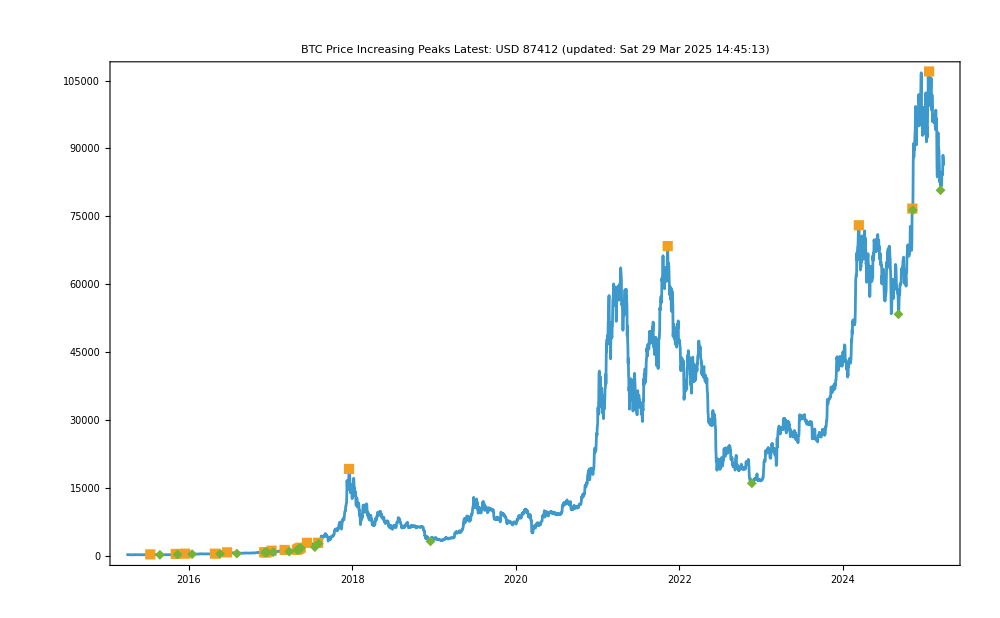

```mathematica
DateListPlot[
{btcusd,First/@ drawdownspct, #[[2]]&/@ drawdownspct}
,Joined->{True,False, False}
,PlotMarkers->{None,Automatic,Automatic}
,ImageSize->imagesize
,GridLines->Automatic
,PlotLabel->Column[
{
Style[
"BTC Price Increasing Peaks"
,titlestyle
]
,Style[
"Latest: USD " <> ToString[btcusd["LastValue"]//Round]
,subtitlestyle
]
,updatedstr
}
,Center
]
]
```